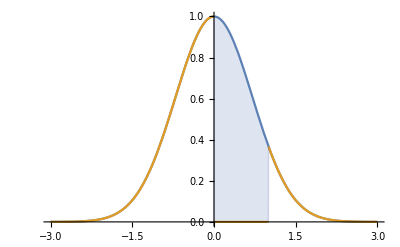

0.746824

```mathematica
(* finding the area of the shaded region *)
(* define lower edge of region so we can use Filling to shade the region *)

f[x_]:=If[x>0 && x<1 ,0,Exp[-x^2]];
Plot[
{Exp[-x^2],f[x]},{x,-3,3},
Filling->{1->{2}}
]
NIntegrate[Exp[-x^2],{x,0,1}]
```

```mathematica
(* finding the length of a Lissajous knot *)

x[t_]:=Cos[2t];
y[t_]:=Cos[3t+π/4];
z[t_]:=Cos[5t+2];

(* Define the knot curve *)
k[t_]:={x[t],y[t],z[t]};
(* Plot the knot *)
ParametricPlot3D[k[t],{t,0,2π},
PlotStyle->Tube[0.03]
]

(* Define the velocity vector *)
velocity[t]=k'[t]
(* the speed is the length of the velocity vector *)
speed[t]=Norm[velocity[t]]
(* integrate the speed to get the length *)
NIntegrate[speed[t],{t,0,2π}]
```

-Graphics3D-

{-2 Sin[2 t],-3 Sin[π/4+3 t],-5 Sin[2+5 t]}

√(4 Abs[Sin[2 t]]^2+9 Abs[Sin[π/4+3 t]]^2+25 Abs[Sin[2+5 t]]^2)

26.4097